## 第十阶数据

第十阶共有12005168个同构类（千万级别），需要分成若干十万级别的数据，逐部分运算，再拼接结果。
读取和计算，大概要一个小时。
注：第九阶274668，读取数据用了47s左右。
第十一阶有1018997864个同构类（十亿级别），光读取数据大概就要两天时间。
总之，8阶内的验算很快捷，第9阶相对从容，第10阶比较勉强。第11阶计算成本高，必不得已时可处理。

```mathematica
Print[12005168/274668*47/60//Ceiling," minutes"];
Print[1018997864/274668*47/60/60//Ceiling," hours"]
```

35 minutes

49 hours

#### 获取部分数据

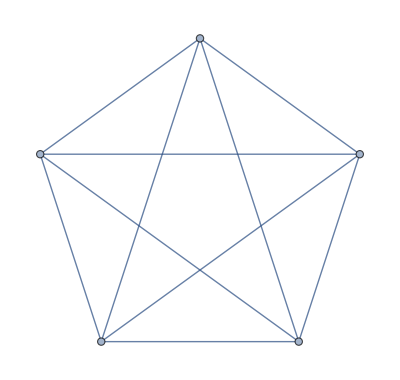

```mathematica
Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph5.g6",{"GraphList",-1}]
```

#### 观察边性质

```mathematica
ec=EdgeCount/@SimpleGraphs[9];
range=ec//DeleteDuplicates;
Count[ec,#]&/@range
Length@%
```

{1,1,2,5,11,25,63,148,345,771,1637,3252,5995,10120,15615,21933,27987,32403,34040,32403,27987,21933,15615,10120,5995,3252,1637,771,345,148,63,25,11,5,2,1,1}

37

#### 获取部分图

```mathematica
m=12005168;
Graph10[a_,b_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph10.g6",{"GraphList",Range[a,b]}];
Graph10[a_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph10.g6",{"GraphList",a}];
```

#### 函数汇总

```mathematica
Needs["IGraphM`"];
Graph10[a_,b_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph10.g6",{"GraphList",Range[a,b]}];
Graph10[a_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph10.g6",{"GraphList",a}];
SimpleGraphs[n_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6"];
(*Graph Subscript[F, k] of 2k+1 vertices (k≥1) *)
GraphF[k_?Positive]:=Module[{vertices1,vertices2,edges},
vertices1=Range@k;
vertices2=Range[-1,-k,-1];
edges=(0<->#&)/@Join[vertices1,vertices2];
edges=Join[edges,Thread[TwoWayRule[Range@k,Range[-1,-k,-1]]]];
Graph@edges];
```

#### 粗筛情况

```mathematica
IsomorphicGraphQ
```

```mathematica
SimpleGraphs[1]
```

Import::nffil: 在 Import 期间没有找到文件 ~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph1.g6.

$Failed